# Quiver Yangian Demo

```mathematica
Print[NotebookDirectory[]]
```

/Users/bpioline/tex/wallcrossing/QuiverYangian/math/

```mathematica
SetDirectory[NotebookDirectory[]];
<<CoulombHiggs`
```

CoulombHiggs 7.0 - A package for evaluating quiver invariants

Computes NCDT invariants for brane tilings following Mozgovoy Reineke 0809.0117, Li Yamazaki 2003.08909 and Descombes 2106.02518
hMat[[i,j,m]] is the weight of the m-th arrow from i to j, subject to vertex and relaxed loop constraints

```mathematica
ListKnownBraneTilings
```

1:C^3

2:Conifold=Y10

3:C^2xC/2

4:C^2xC/3

5:C^3/2x2

6:SPP=L121

7:L131

8:P2=C^3/(1,1,1)

9:F0.1=P1xP1

10:F0.2=P1xP1

11:F1=dP1=Y21=L312

12:F2=C^3/(1,1,2)

13:dP2.1

14:dP2.2

15:dP3.1

16:dP3.2

17:dP3.3

18:dP3.4

19:PdP2

20:PdP3a=C^3/(1,2,3)

21:PdP3b

22:PdP3c=SPP/2

23:PdP4a

24:PdP4b

25:PdP5a=Conifold/2x2

26:PdP5b=L131/2

27:PdP5c=C3/4x2

28:PdP6=C3/3x3

29:L152

30:Y32=L153

31:C^3/(1,1,3)

32:C^3/(1,1,4)

```mathematica
$QuiverVertexLabels={};{Tiling,Fan,hMat,Wp,Wm,v1,v2}=BraneTilingsData[[10]];Tiling
```

F0.2=P1xP1

```mathematica
(* label vertices from 0 to K-1 *) 
$QuiverVertexLabels=Range[0,Length[hMat]-1];
```

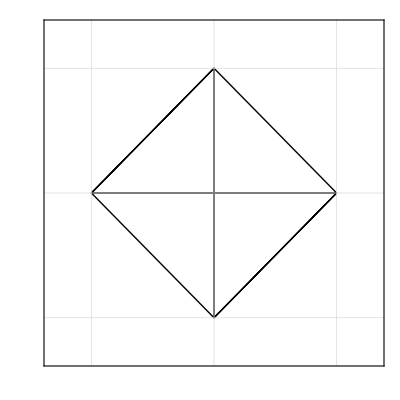
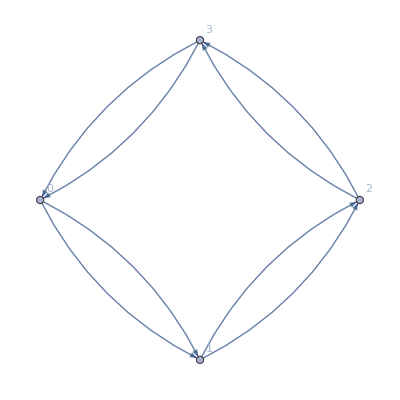
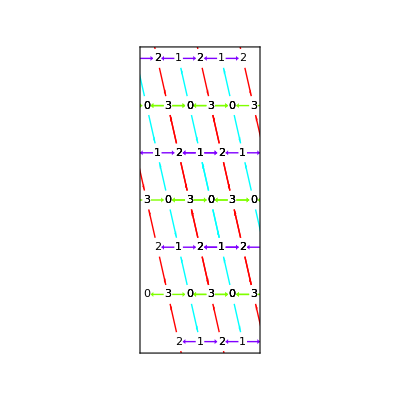

```mathematica
L=2.7;{PlotToricFan[Fan],PlotQuiver[hMat],PlotTiling[hMat,8,{v1,v2},{{-L-.5,L-.5},{-L,L}},.2]}
```

```mathematica
(* recompute height matrix such that h(Phi_{1,2}^1)=h1, h(Phi_{2,3}^1)=h2 *)
hMat=HeightMatrixFromPotential[Wp,Wm,{1,2,1},{2,3,1}]
```

{{{},{h1,-h1+h3/2},{},{}},{{},{},{h2,-h2+h3/2},{}},{{},{},{},{h1,-h1+h3/2}},{{h2,-h2+h3/2},{},{},{}}}

```mathematica
PlotTiling3D[hMat,10,{{1,0,0},{0,1,0},{0,2,2}},5,{}]
```

-Graphics3D-

## Get the fan from the quiver

```mathematica
ExternalPoints[DualFan[hMat,Wp,Wm]]
```

{{1,0},{0,1},{-1,0},{0,-1}}

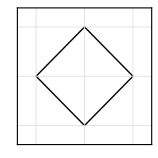

```mathematica
PlotToricFan[%]
```

We can also directly study the correspondence between the fan and the quiver, by computing the weight associated to a side of the fan or by computing the arrows associated to a corner of the fan

```mathematica
SideWeight[hMat,Wp,Wm,1]
```

-2 h1-2 h2+2 h3

```mathematica
D4FramingDictionary[hMat,Wp,Wm][[1]]
```

{{1,2,1},{3,4,1}}

## Evaluate the partition function of framed NCDT invariants using Quiver Yangian algorithm

We can compute unrefined and refined D6 framed NCDT invariants. The unrefined series are given as a polynomial in term of y, where y should be replaced by 1 to get the unrefined invariant and replaced by -1 to get the raw counting of molten crystals. It is important to highlight that this y is not a refinement, only a variable interpolating between the unrefined serie and the molten crystal count.

```mathematica
Nn=7; (* substitute y=1 to get unrefined, y=-1 to get raw counting *)
Z1=UnrefinedSeriesFromCrystal[hMat,D6Framing[hMat,1],Nn]
```

1+x_1-2 y x_1 x_2+x_1 x_2^2+4 y^2 x_1 x_2 x_3-4 y^3 x_1 x_2^2 x_3-2 y x_1 x_2 x_3^2+6 y^4 x_1 x_2^2 x_3^2-4 y^3 x_1 x_2^2 x_3^3+x_1 x_2^2 x_3^4-4 y^5 x_1 x_2 x_3 x_4-4 y^7 x_1^2 x_2 x_3 x_4+4 y^6 x_1 x_2^2 x_3 x_4+8 y^10 x_1^2 x_2^2 x_3 x_4-4 y^11 x_1^2 x_2^3 x_3 x_4+4 y^6 x_1 x_2 x_3^2 x_4+4 y^8 x_1^2 x_2 x_3^2 x_4-14 y^9 x_1 x_2^2 x_3^2 x_4-22 y^13 x_1^2 x_2^2 x_3^2 x_4+16 y^10 x_1 x_2^2 x_3^3 x_4-2 y^9 x_1 x_2 x_3^2 x_4^2-6 y^13 x_1^2 x_2 x_3^2 x_4^2+10 y^12 x_1 x_2^2 x_3^2 x_4^2

```mathematica
Zref=D6FramedNCDTSeries[hMat,Wp,Wm,1,Nn]
```

1+x_1+(-1/y-y) x_1 x_2+x_1 x_2^2+(2+1/y^2+y^2) x_1 x_2 x_3+(-1/y^3-1/y-y-y^3) x_1 x_2^2 x_3+(-1/y-y) x_1 x_2 x_3^2+(2+1/y^4+1/y^2+y^2+y^4) x_1 x_2^2 x_3^2+(-1/y^3-1/y-y-y^3) x_1 x_2^2 x_3^3+x_1 x_2^2 x_3^4+(-1/y-2 y-y^3) x_1 x_2 x_3 x_4+(-1/y-2 y-y^3) x_1^2 x_2 x_3 x_4+(2+1/y^2+y^2) x_1 x_2^2 x_3 x_4+(3+1/y^2+3 y^2+y^4) x_1^2 x_2^2 x_3 x_4+(-1/y-2 y-y^3) x_1^2 x_2^3 x_3 x_4+(2+1/y^2+y^2) x_1 x_2 x_3^2 x_4+(2+1/y^2+y^2) x_1^2 x_2 x_3^2 x_4+(-1/y^5-2/y^3-4/y-4 y-2 y^3-y^5) x_1 x_2^2 x_3^2 x_4+(-2/y^3-6/y-8 y-5 y^3-y^5) x_1^2 x_2^2 x_3^2 x_4+(4+1/y^6+2/y^4+3/y^2+3 y^2+2 y^4+y^6) x_1 x_2^2 x_3^3 x_4+(-1/y-y) x_1 x_2 x_3^2 x_4^2+(-1/y^3-2/y-2 y-y^3) x_1^2 x_2 x_3^2 x_4^2+(4+1/y^4+2/y^2+2 y^2+y^4) x_1 x_2^2 x_3^2 x_4^2

```mathematica
(Z1/.y->1)-(Zref/.y->1)
```

0

We can also compute unrefined and refined D4 framed NCDT invariants. Similarly, the y variable returned by UnrefinedSeriesFromCrystal is not a refinement variable.

```mathematica
Z1=UnrefinedSeriesFromCrystal[hMat,D4Framing[hMat,1,2,1],Nn]
```

1+x_1+2 x_1 x_2+(x_1 x_2^2)/y^2-4 y x_1 x_2 x_3-4 y x_1 x_2^2 x_3+2 x_1 x_2 x_3^2+6 y^2 x_1 x_2^2 x_3^2-4 y x_1 x_2^2 x_3^3+(x_1 x_2^2 x_3^4)/y^2+4 y^4 x_1 x_2 x_3 x_4+4 y^6 x_1^2 x_2 x_3 x_4+4 y^4 x_1 x_2^2 x_3 x_4+8 y^8 x_1^2 x_2^2 x_3 x_4+4 y^8 x_1^2 x_2^3 x_3 x_4-4 y^5 x_1 x_2 x_3^2 x_4-4 y^7 x_1^2 x_2 x_3^2 x_4-14 y^7 x_1 x_2^2 x_3^2 x_4-22 y^11 x_1^2 x_2^2 x_3^2 x_4+16 y^8 x_1 x_2^2 x_3^3 x_4+2 y^8 x_1 x_2 x_3^2 x_4^2+6 y^12 x_1^2 x_2 x_3^2 x_4^2+10 y^10 x_1 x_2^2 x_3^2 x_4^2

```mathematica
Zref=D4FramedNCDTSeries[hMat,Wp,Wm,1,2,1,Nn]
```

1+x_1+2 x_1 x_2+x_1 x_2^2+(-2/y-2 y) x_1 x_2 x_3+(-1/y^3-1/y-y-y^3) x_1 x_2^2 x_3+2 x_1 x_2 x_3^2+(2+1/y^4+1/y^2+y^2+y^4) x_1 x_2^2 x_3^2+(-1/y^3-1/y-y-y^3) x_1 x_2^2 x_3^3+x_1 x_2^2 x_3^4+(2+1/y^2+y^2) x_1 x_2 x_3 x_4+(2+1/y^2+y^2) x_1^2 x_2 x_3 x_4+(2+1/y^2+y^2) x_1 x_2^2 x_3 x_4+(4+2/y^2+2 y^2) x_1^2 x_2^2 x_3 x_4+(2+1/y^2+y^2) x_1^2 x_2^3 x_3 x_4+(-2/y-2 y) x_1 x_2 x_3^2 x_4+(-2/y-2 y) x_1^2 x_2 x_3^2 x_4+(-1/y^5-2/y^3-4/y-4 y-2 y^3-y^5) x_1 x_2^2 x_3^2 x_4+(-3/y^3-8/y-8 y-3 y^3) x_1^2 x_2^2 x_3^2 x_4+(4+1/y^6+2/y^4+3/y^2+3 y^2+2 y^4+y^6) x_1 x_2^2 x_3^3 x_4+2 x_1 x_2 x_3^2 x_4^2+(2+2/y^2+2 y^2) x_1^2 x_2 x_3^2 x_4^2+(4+1/y^4+2/y^2+2 y^2+y^4) x_1 x_2^2 x_3^2 x_4^2

```mathematica
(Z1/.y->1)-(Zref/.y->1)
```

0

## Construct perfect matchings, and look for pairs of disjoint cuts

```mathematica
Perf=ListPerfectMatchings[Wp,Wm];LiDoubleCuts=Drop[Union[Flatten[Table[If[Intersection[Perf[[i]],Perf[[j]]]=={},{i,j},{}],{i,Length[Perf]},{j,i+1,Length[Perf]}],1]],1]
```

{{1,4},{1,5},{1,6},{1,7},{1,8},{2,3},{2,4},{2,5},{2,6},{2,8},{3,4},{3,5},{3,6},{3,8},{4,7},{4,8},{5,6},{5,7},{6,7},{7,8}}

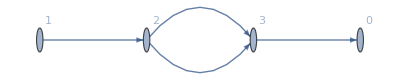
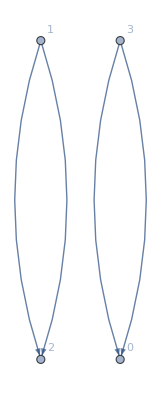
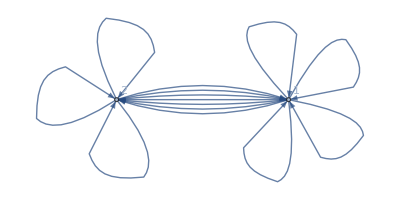
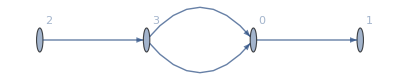
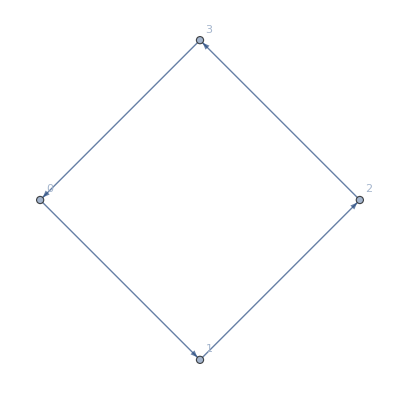
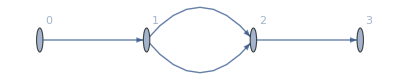
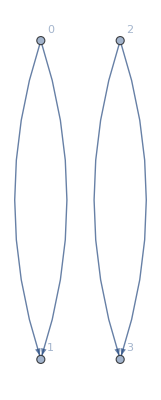
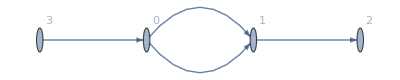
{{{1,4},Graph[{3→4,3→4,4→1,4→1},DirectedEdges→True,VertexLabels→{1→0,2→1,3→2,4→3}],{}},{{1,5},-Graphics-,{}},{{1,6},-Graphics-,{}},{{1,7},-Graphics-,{}},{{1,8},Graph[{2→3,2→3,3→4,3→4},DirectedEdges→True,VertexLabels→{1→0,2→1,3→2,4→3}],{}},{{2,3},-Graphics-,{}},{{2,4},-Graphics-,{}},{{2,5},-Graphics-,{{{1,2,3,4},4}}},{{2,6},-Graphics-,{{{1,2,3,4},4}}},{{2,8},-Graphics-,{}},{{3,4},-Graphics-,{}},{{3,5},-Graphics-,{{{1,2,3,4},4}}},{{3,6},-Graphics-,{{{1,2,3,4},4}}},{{3,8},-Graphics-,{}},{{4,7},Graph[{1→2,1→2,4→1,4→1},DirectedEdges→True,VertexLabels→{1→0,2→1,3→2,4→3}],{}},{{4,8},-Graphics-,{}},{{5,6},-Graphics-,{}},{{5,7},-Graphics-,{}},{{6,7},-Graphics-,{}},{{7,8},Graph[{1→2,1→2,2→3,2→3},DirectedEdges→True,VertexLabels→{1→0,2→1,3→2,4→3}],{}}}

```mathematica
Table[hMat2=Delete[hMat,Perf[[LiDoubleCuts[[i,1]]]]];
hMat3=Delete[hMat2,Perf[[LiDoubleCuts[[i,2]]]]];{LiDoubleCuts[[i]],PlotQuiver[hMat3],ListLoopRCharges[HeightMatrixToDSZ[hMat3],HeightMatrixToDSZ[hMat3]]},{i,Length[LiDoubleCuts]}]
```

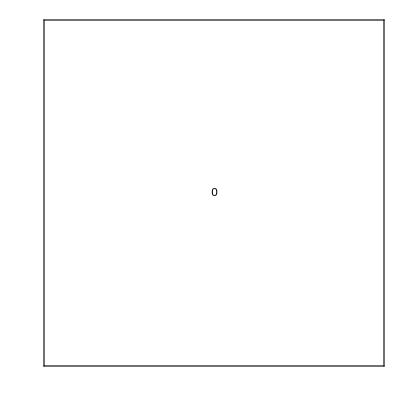
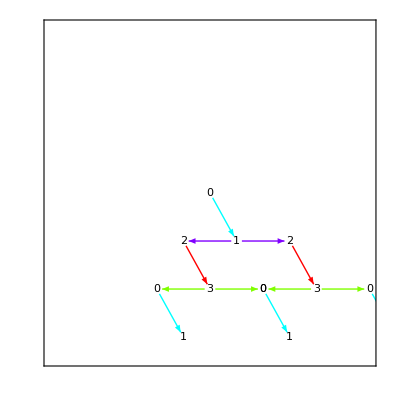
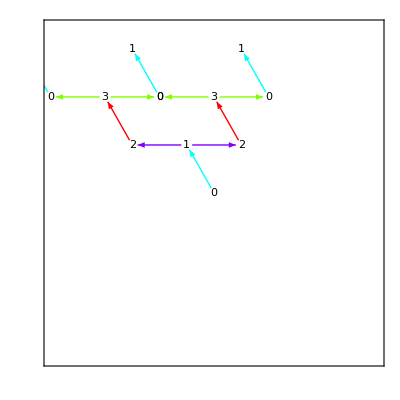
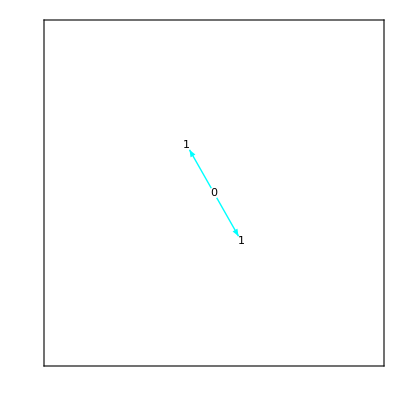
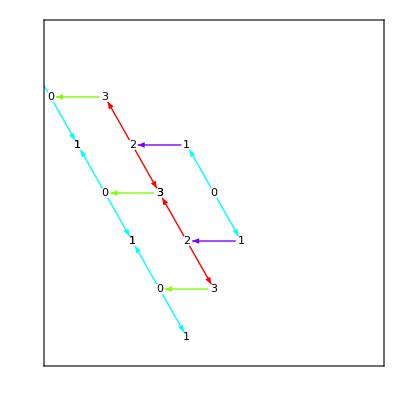
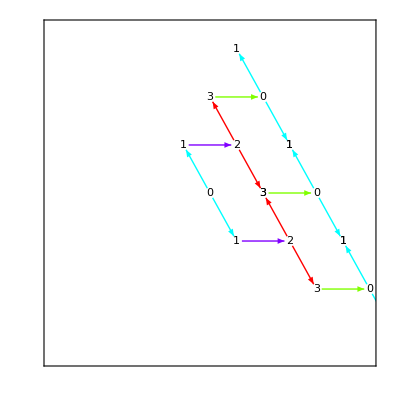
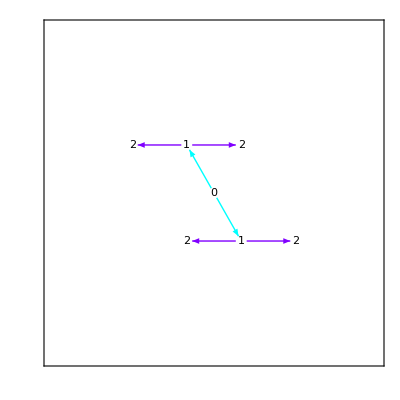
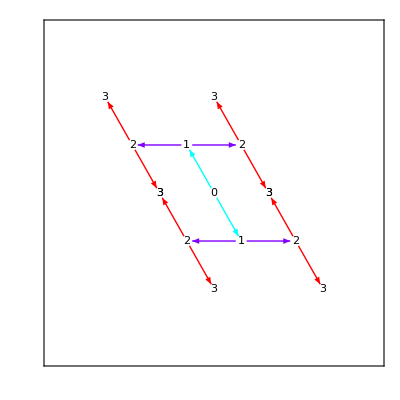
{{{{1,2,1},{1,2,2}},-Graphics-,-Graphics3D-},{{{1,2,1},{3,4,1}},-Graphics-,-Graphics3D-},{{{1,2,2},{3,4,2}},-Graphics-,-Graphics3D-},{{{2,3,1},{2,3,2}},-Graphics-,-Graphics3D-},{{{2,3,1},{4,1,1}},-Graphics-,-Graphics3D-},{{{2,3,2},{4,1,2}},-Graphics-,-Graphics3D-},{{{3,4,1},{3,4,2}},-Graphics-,-Graphics3D-},{{{4,1,1},{4,1,2}},-Graphics-,-Graphics3D-}}

```mathematica
Table[{Perf[[i]],
PlotTiling[hMat,5,{v1,v2},{{-3,3},{-3,3}},.1,Perf[[i]]],PlotTiling3D[hMat,5,{{1,0,0},{0,1,0},{0,0,1}},{{-3,3},{-3,3},{-3,3}},Perf[[i]]]}
,{i,Length[Perf]}]
```